```mathematica
MakeGraph[list_]:=Block[{i=0, node},
Graph[
With[{g=
Graph[
Flatten[
Table[
i=i+1;
node="x"<>ToString[e[[2]]]<>"-"<>ToString[e[[3]]];
{node<->e[[1]],e[[2]]<->node,e[[3]]<->node}
(*{e[[2]]<->e[[1]],e[[3]]<->e[[1]]}*)
,{e,list}
]
]
]},
g
],
VertexLabels->"Name",
ImageSize->800
]
(*{l,{"CircularEmbedding","SpiralEmbedding","SpringEmbedding","SpringElectricalEmbedding","HighDimensionalEmbedding","CircularMultipartiteEmbedding","DiscreteSpiralEmbedding","GridEmbedding","LinearEmbedding","MultipartiteEmbedding","StarEmbedding","BalloonEmbedding","RadialEmbedding","LayeredDigraphEmbedding","LayeredEmbedding","TutteEmbedding"}}*)

]
```

```mathematica
MakeGraph[list_]:=Block[{i=0, node},
Table[
i=i+1;
node="x"<>ToString[e[[2]]]<>"-"<>ToString[e[[3]]];
{node<->e[[1]],e[[2]]<->node,e[[3]]<->node}
(*{e[[2]]<->e[[1]],e[[3]]<->e[[1]]}*)
,{e,list}
]
]
```

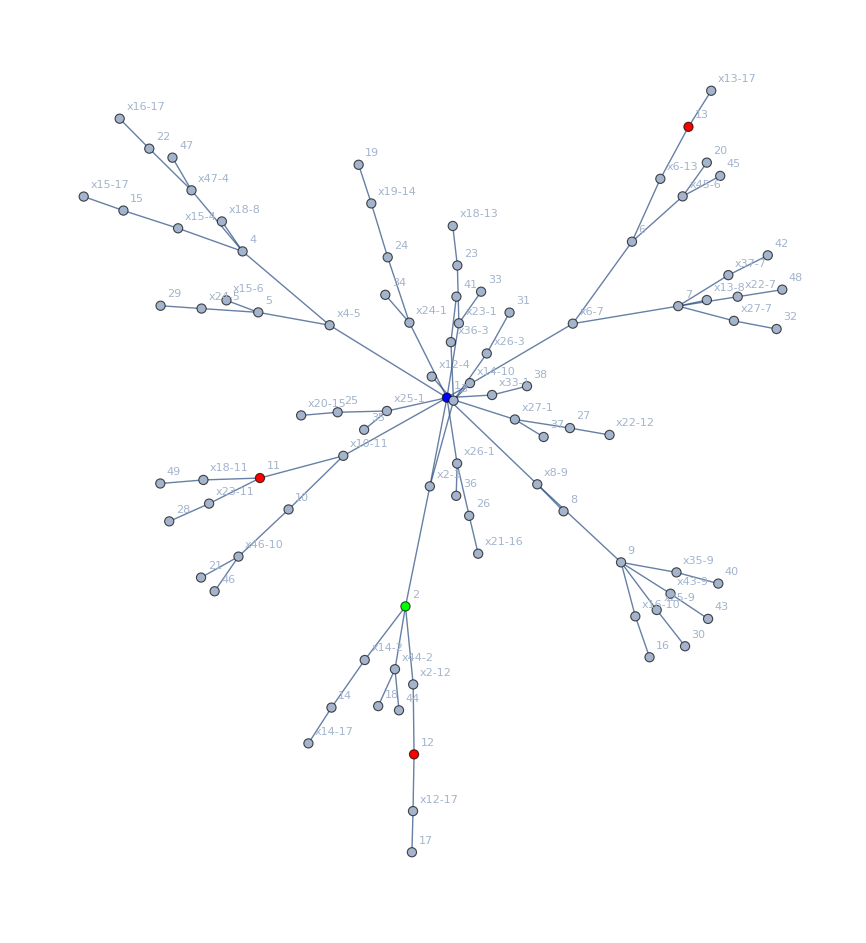

```mathematica
Graph[
FindSpanningTree[MakeGraph[{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},
{5,2,12},{8,6,13},{3,14,10},{5,15,6},{9,16,10},
{18,12,17},{19,13,17},{20,14,17},{21,15,17},{22,16,17},
{23,18,13},{24,19,14},{25,20,15},
{26,21,16},{27,22,12},{28,23,11},{29,24,5},
{30,25,9},{31,26,3},{32,27,7},{33,23,1},
{34,24,1},{35,25,1},{36,26,1},{37,27,1},{38,33,1},{40,35,9},{41,36,3},{42,37,7},{18,43,9},{18,44,2},{20,45,6},{21,46,10},{22,47,4},{48,22,7},{49,18,11},{3,12,4},{7,13,8},{11,14,2},{7,15,4},{4,18,8}}]]
,VertexStyle->{11->Red,12->Red,13->Red,1->Blue,2->Green}, VertexLabels->"Name"]
```

```mathematica
Sort[{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},
{5,2,12},{8,6,13},{3,14,10},{5,15,6},{9,16,10},
{18,12,17},{19,13,17},{20,14,17},{21,15,17},{22,16,17},
{23,18,13},{24,19,14},{25,20,15},
{26,21,16},{27,22,12},{28,23,11},{29,24,5},
{30,25,9},{31,26,3},{32,27,7},{33,23,1},
{34,24,1},{35,25,1},{36,26,1},{37,27,1},{38,33,1},{40,35,9},{41,36,3},{42,37,7},{18,43,9},{18,44,2},{20,45,6},{21,46,10},{22,47,4},{48,22,7},{49,18,11},{3,12,4},{7,13,8},{11,14,2},{7,15,4},{4,18,8}}]//TableForm
```

1 | 2 | 3
1 | 4 | 5
1 | 6 | 7
1 | 8 | 9
1 | 10 | 11
3 | 12 | 4
3 | 14 | 10
4 | 18 | 8
5 | 2 | 12
5 | 15 | 6
7 | 13 | 8
7 | 15 | 4
8 | 6 | 13
9 | 16 | 10
11 | 14 | 2
18 | 12 | 17
18 | 43 | 9
18 | 44 | 2
19 | 13 | 17
20 | 14 | 17
20 | 45 | 6
21 | 15 | 17
21 | 46 | 10
22 | 16 | 17
22 | 47 | 4
23 | 18 | 13
24 | 19 | 14
25 | 20 | 15
26 | 21 | 16
27 | 22 | 12
28 | 23 | 11
29 | 24 | 5
30 | 25 | 9
31 | 26 | 3
32 | 27 | 7
33 | 23 | 1
34 | 24 | 1
35 | 25 | 1
36 | 26 | 1
37 | 27 | 1
38 | 33 | 1
40 | 35 | 9
41 | 36 | 3
42 | 37 | 7
48 | 22 | 7
49 | 18 | 11

```mathematica
MakeEq[list_]:=Block[{x1,x2,x3},
Table[
x1=Symbol["x"<>ToString[e[[1]]]];
x2=Symbol["x"<>ToString[e[[2]]]];
x3=Symbol["x"<>ToString[e[[3]]]];
x1==x2+x3
,{e,list}
]
]
```

```mathematica
Fold[And,MakeEq[{{1,2,3},{1,4,5},{1,6,7},{1,8,9},{1,10,11},
{5,2,12},{8,6,13},{3,14,10},{5,15,6},{9,16,10},
{18,12,17},{19,13,17},{20,14,17},{21,15,17},{22,16,17},
{23,18,13},{24,19,14},{25,20,15},
{26,21,16},{27,22,12},{28,23,11},{29,24,5},
{30,25,9},{31,26,3},{32,27,7},{33,23,1},
{34,24,1},{35,25,1},{36,26,1},{37,27,1},{38,33,1},{40,35,9},{41,36,3},{42,37,7},{18,43,9},{18,44,2},{20,45,6},{21,46,10},{22,47,4},{48,22,7},{49,18,11},{3,12,4},{7,13,8},{11,14,2},{7,15,4},{4,18,8},
{55,50,2},{56,54,2}}]]
```

x56==2 x54&&x56==x4+x5&&x56==x6+x7&&x56==x8+x9&&x56==x10+x11&&x5==x10+x12&&x8==x13+x6&&x13==x10+x14&&x5==x15+x6&&x9==x10+x16&&x18==x12+x17&&x19==x13+x17&&x20==x14+x17&&x21==x15+x17&&x22==x16+x17&&x23==x13+x18&&x24==x14+x19&&x25==x15+x20&&x26==x16+x21&&x27==x12+x22&&x28==x11+x23&&x29==x24+x5&&x30==x25+x9&&x31==x26+x9&&x32==x27+x7&&x33==x23+x33&&x34==x24+x34&&x35==x25+x35&&x36==x26+x36&&x37==x27+x37&&x38==x33+x38&&x40==x35+x9&&x41==x36+x9&&x42==x37+x7&&x18==x43+x9&&x18==2 x44&&x20==x45+x6&&x21==x10+x46&&x22==x4+x47&&x48==x22+x7&&x49==x11+x18&&x11==x12+x4&&x7==x13+x8&&x11==2 x14&&x7==x15+x4&&x4==x18+x8&&x55==2 x50&&x56==2 x54

```mathematica
Reduce[x56==2 x54&&x56==x4+x5&&x56==x6+x7&&x56==x8+x9&&x56==x10+x11&&x5==x10+x12&&x8==x13+x6&&x13==x10+x14&&x5==x15+x6&&x9==x10+x16&&x18==x12+x17&&x19==x13+x17&&x20==x14+x17&&x21==x15+x17&&x22==x16+x17&&x23==x13+x18&&x24==x14+x19&&x25==x15+x20&&x26==x16+x21&&x27==x12+x22&&x28==x11+x23&&x29==x24+x5&&x30==x25+x9&&x31==x26+x9&&x32==x27+x7&&x33==x23+x33&&x34==x24+x34&&x35==x25+x35&&x36==x26+x36&&x37==x27+x37&&x38==x33+x38&&x40==x35+x9&&x41==x36+x9&&x42==x37+x7&&x18==x43+x9&&x18==2 x44&&x20==x45+x6&&x21==x10+x46&&x22==x4+x47&&x48==x22+x7&&x49==x11+x18&&x11==x12+x4&&x7==x13+x8&&x11==2 x14&&x7==x15+x4&&x4==x18+x8&&x55==x2+ x50&&x56==2 x54&&x17==x1-x122-x13-x11,x50]
```

x33==0&&x9==0&&x8==0&&x7==0&&x6==0&&x56==0&&x54==0&&x5==0&&x49==0&&x48==0&&x47==0&&x46==0&&x45==0&&x44==0&&x43==0&&x4==0&&x37==x42&&x36==x41&&x35==x40&&x32==0&&x31==0&&x30==0&&x29==0&&x28==0&&x27==0&&x26==0&&x25==0&&x24==0&&x23==0&&x22==0&&x21==0&&x20==0&&x19==0&&x18==0&&x17==0&&x16==0&&x15==0&&x14==0&&x13==0&&x12==0&&x11==0&&x10==0&&x1==x122&&x50==-x2+x55